```mathematica
Ship=Import["C:\\Users\\memoa\\Downloads\\shippingtable.csv"];
Labels=Ship[[1]];
Ship=Delete[Ship,1];
L=Length[Ship];

TotalXCust=Shipᵀ[[{3,1}]]ᵀ;
TotalXCustRate=Table[{Ship[[i,3]],Ship[[i,1]]/Ship[[i,3]]},{i,1,L}];

maxTotal=Max[Table[Ship[[i,3]],{i,1,L}]];
m=Mean[TotalXCustRateᵀ[[2]]];
ScaledTotalXCust={TotalXCustᵀ[[1]],Map[#/m&,TotalXCustᵀ[[2]]]}ᵀ;
ScaledTotalXCustRate={Map[#/maxTotal/2&,TotalXCustRateᵀ[[1]]],TotalXCustRateᵀ[[2]]}ᵀ;
```

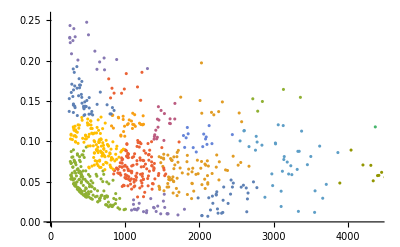

```mathematica
ListPlot[FindClusters[TotalXCustRate,Method->"MeanShift"]]
```